## Setup

```mathematica
Remove["args"]
FR$Parallel=False;
$FeynRulesPath=SetDirectory["/Users/laramason/FeynRules/feynrules-current"];
<<FeynRules`;


SetDirectory[$FeynRulesPath<>"/Models/U(1)-project"];
LoadModel["sm.fr","ch_ps.fr"];
LoadRestriction["DiagonalCKM.rst"] (*,"Massless.rst"]*)
```

- FeynRules -

Version: 2.3.34 ( 22 May 2019).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

L. Mason

B. Fuks

Model Version: 1.1

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model CHpseudo loaded.

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

## Lagrangian playground

In Feynman gauge: no ghosts and no goldstones

```mathematica
CheckMassSpectrum[LPSeudo+LSM]
```

```mathematica
CheckHermiticity[ExpandIndices[LPSeudo + LSM]/.{(G0|GP|GPbar)->0}]
```

Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].

If the lagrangian is hermitian, then the number of vertices should be zero.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

No vertices found.

0 vertices obtained.

The lagrangian is hermitian.

{}

```mathematica
WriteUFO[ExpandIndices[LPSeudo],ExpandIndices[LSM],AddDecays->False, Output->"CHPS_UFO_FF_withtau"]
```

```mathematica
Assuming[Element[yd[__]|yu[__]|yl[__],Reals],
Simplify[FeynmanRules[
OptimizeIndex[ExpandIndices[LPSeudo + LSM]/.{(G0|GP|GPbar)->0}]
]/.{Eps[indx__]:>Signature[{indx}] Eps[Sequence@@Sort[{indx}]]}]
]
```

## Calculation of branching ratios

```mathematica
vertices = FeynmanRules[LSM]
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

98 possible non-zero vertices have been found -> starting the computation:  / 98.

93 vertices obtained.

{{{{G0,1},{G0,2},{G0,3},{G0,4}},-6 ⅈ lam},{{{G0,1},{G0,2},{GP,3},{GP^†,4}},-2 ⅈ lam},{{{GP,1},{GP,2},{GP^†,3},{GP^†,4}},-4 ⅈ lam},{{{G0,1},{G0,2},{H,3},{H,4}},-2 ⅈ lam},{{{GP,1},{GP^†,2},{H,3},{H,4}},-2 ⅈ lam},{{{H,1},{H,2},{H,3},{H,4}},-6 ⅈ lam},{{{G0,1},{G0,2},{H,3}},-2 ⅈ lam vev},{{{GP,1},{GP^†,2},{H,3}},-2 ⅈ lam vev},{{{H,1},{H,2},{H,3}},-6 ⅈ lam vev},{{{A,1},{A,2},{GP,3},{GP^†,4}},2 ⅈ e^2 η_(μ_1,μ_2)},{{{A,1},{GP,2},{GP^†,3}},ⅈ e p_2^μ_1-ⅈ e p_3^μ_1},{{{ghA^†,1},{ghWm,2},{W,3}},ⅈ e p_2^μ_3+ⅈ e p_3^μ_3},{{{ghA^†,1},{ghWp,2},{W^†,3}},-ⅈ e p_2^μ_3-ⅈ e p_3^μ_3},{{{ghWm^†,1},{ghA,2},{GP^†,3}},(e^2 vev)/(2 s_w)},{{{ghWm^†,1},{ghA,2},{W^†,3}},ⅈ e p_2^μ_3+ⅈ e p_3^μ_3},{{{ghWm^†,1},{ghWm,2},{G0,3}},-(e^2 vev)/(4 s_w^2)},{{{ghWm^†,1},{ghWm,2},{H,3}},-(ⅈ e^2 vev)/(4 s_w^2)},{{{ghWm^†,1},{ghWm,2},{A,3}},-ⅈ e p_2^μ_3-ⅈ e p_3^μ_3},{{{ghWm^†,1},{ghWm,2},{Z,3}},-(ⅈ c_w e p_2^μ_3)/s_w-(ⅈ c_w e p_3^μ_3)/s_w},{{{ghWm^†,1},{ghZ,2},{GP^†,3}},-(e^2 vev)/(4 c_w)+(c_w e^2 vev)/(4 s_w^2)},{{{ghWm^†,1},{ghZ,2},{W^†,3}},(ⅈ c_w e p_2^μ_3)/s_w+(ⅈ c_w e p_3^μ_3)/s_w},{{{ghWp^†,1},{ghA,2},{GP,3}},-(e^2 vev)/(2 s_w)},{{{ghWp^†,1},{ghA,2},{W,3}},-ⅈ e p_2^μ_3-ⅈ e p_3^μ_3},{{{ghWp^†,1},{ghWp,2},{G0,3}},(e^2 vev)/(4 s_w^2)},{{{ghWp^†,1},{ghWp,2},{H,3}},-(ⅈ e^2 vev)/(4 s_w^2)},{{{ghWp^†,1},{ghWp,2},{A,3}},ⅈ e p_2^μ_3+ⅈ e p_3^μ_3},{{{ghWp^†,1},{ghWp,2},{Z,3}},(ⅈ c_w e p_2^μ_3)/s_w+(ⅈ c_w e p_3^μ_3)/s_w},{{{ghWp^†,1},{ghZ,2},{GP,3}},(e^2 vev)/(4 c_w)-(c_w e^2 vev)/(4 s_w^2)},{{{ghWp^†,1},{ghZ,2},{W,3}},-(ⅈ c_w e p_2^μ_3)/s_w-(ⅈ c_w e p_3^μ_3)/s_w},{{{ghZ^†,1},{ghWm,2},{GP,3}},(e^2 vev)/(4 c_w)+(c_w e^2 vev)/(4 s_w^2)},{{{ghZ^†,1},{ghWm,2},{W,3}},(ⅈ c_w e p_2^μ_3)/s_w+(ⅈ c_w e p_3^μ_3)/s_w},{{{ghZ^†,1},{ghWp,2},{GP^†,3}},-(e^2 vev)/(4 c_w)-(c_w e^2 vev)/(4 s_w^2)},{{{ghZ^†,1},{ghWp,2},{W^†,3}},-(ⅈ c_w e p_2^μ_3)/s_w-(ⅈ c_w e p_3^μ_3)/s_w},{{{ghZ^†,1},{ghZ,2},{H,3}},-1/2 ⅈ e^2 vev-(ⅈ c_w^2 e^2 vev)/(4 s_w^2)-(ⅈ e^2 s_w^2 vev)/(4 c_w^2)},{{{ghG^†,1},{ghG,2},{G,3}},g_s f_(a_3,a_1,a_2) p_2^μ_3+g_s f_(a_3,a_1,a_2) p_3^μ_3},{{{G,1},{G,2},{G,3}},g_s f_(a_1,a_2,a_3) p_1^μ_3 η_(μ_1,μ_2)-g_s f_(a_1,a_2,a_3) p_2^μ_3 η_(μ_1,μ_2)-g_s f_(a_1,a_2,a_3) p_1^μ_2 η_(μ_1,μ_3)+g_s f_(a_1,a_2,a_3) p_3^μ_2 η_(μ_1,μ_3)+g_s f_(a_1,a_2,a_3) p_2^μ_1 η_(μ_2,μ_3)-g_s f_(a_1,a_2,a_3) p_3^μ_1 η_(μ_2,μ_3)},{{{G,1},{G,2},{G,3},{G,4}},ⅈ g_s^2 f_(a_1,a_3,Gluon$1) f_(a_2,a_4,Gluon$1) η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ g_s^2 f_(a_1,a_2,Gluon$1) f_(a_3,a_4,Gluon$1) η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ g_s^2 f_(a_1,a_4,Gluon$1) f_(a_2,a_3,Gluon$1) η_(μ_1,μ_3) η_(μ_2,μ_4)-ⅈ g_s^2 f_(a_1,a_2,Gluon$1) f_(a_3,a_4,Gluon$1) η_(μ_1,μ_3) η_(μ_2,μ_4)-ⅈ g_s^2 f_(a_1,a_4,Gluon$1) f_(a_2,a_3,Gluon$1) η_(μ_1,μ_2) η_(μ_3,μ_4)-ⅈ g_s^2 f_(a_1,a_3,Gluon$1) f_(a_2,a_4,Gluon$1) η_(μ_1,μ_2) η_(μ_3,μ_4)},{{{uq^-,1},{dq,2},{GP,3}},(V^CKM)_(Generation$1,f_2) (y^u)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2)-(V^CKM)_(f_1,Generation$1) δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(Generation$1,f_2)},{{{uq^-,1},{uq,2},{G0,3}},((y^u)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2)-(δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(f_1,f_2))/(√2)},{{{uq^-,1},{uq,2},{H,3}},-(ⅈ (y^u)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2)-(ⅈ δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(f_1,f_2))/(√2)},{{{dq^-,1},{uq,2},{GP^†,3}},(V^CKM)_(f_2,Generation$1)^* (y^d)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2)-(V^CKM)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(Generation$1,f_2)},{{{dq^-,1},{dq,2},{G0,3}},-((y^d)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2)+(δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(f_1,f_2))/(√2)},{{{dq^-,1},{dq,2},{H,3}},-(ⅈ (y^d)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2)-(ⅈ δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(f_1,f_2))/(√2)},{{{l^-,1},{vl,2},{GP^†,3}},(y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2)},{{{l^-,1},{l,2},{G0,3}},-((y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2))/(√2)+((P_+)_(s_1,s_2) (y^l)_(f_1,f_2))/(√2)},{{{l^-,1},{l,2},{H,3}},-(ⅈ (y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2))/(√2)-(ⅈ (P_+)_(s_1,s_2) (y^l)_(f_1,f_2))/(√2)},{{{A,1},{G0,2},{GP^†,3},{W,4}},-(ⅈ e^2 η_(μ_1,μ_4))/(2 s_w)},{{{A,1},{GP^†,2},{H,3},{W,4}},-(e^2 η_(μ_1,μ_4))/(2 s_w)},{{{A,1},{GP^†,2},{W,3}},-(e^2 vev η_(μ_1,μ_3))/(2 s_w)},{{{G0,1},{GP^†,2},{W,3}},-(ⅈ e p_1^μ_3)/(2 s_w)+(ⅈ e p_2^μ_3)/(2 s_w)},{{{GP^†,1},{H,2},{W,3}},(e p_1^μ_3)/(2 s_w)-(e p_2^μ_3)/(2 s_w)},{{{A,1},{W,2},{W^†,3}},-ⅈ e p_1^μ_3 η_(μ_1,μ_2)+ⅈ e p_2^μ_3 η_(μ_1,μ_2)+ⅈ e p_1^μ_2 η_(μ_1,μ_3)-ⅈ e p_3^μ_2 η_(μ_1,μ_3)-ⅈ e p_2^μ_1 η_(μ_2,μ_3)+ⅈ e p_3^μ_1 η_(μ_2,μ_3)},{{{A,1},{G0,2},{GP,3},{W^†,4}},-(ⅈ e^2 η_(μ_1,μ_4))/(2 s_w)},{{{A,1},{GP,2},{H,3},{W^†,4}},(e^2 η_(μ_1,μ_4))/(2 s_w)},{{{A,1},{GP,2},{W^†,3}},(e^2 vev η_(μ_1,μ_3))/(2 s_w)},{{{G0,1},{GP,2},{W^†,3}},(ⅈ e p_1^μ_3)/(2 s_w)-(ⅈ e p_2^μ_3)/(2 s_w)},{{{GP,1},{H,2},{W^†,3}},(e p_1^μ_3)/(2 s_w)-(e p_2^μ_3)/(2 s_w)},{{{G0,1},{G0,2},{W,3},{W^†,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 s_w^2)},{{{GP,1},{GP^†,2},{W,3},{W^†,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 s_w^2)},{{{H,1},{H,2},{W,3},{W^†,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 s_w^2)},{{{H,1},{W,2},{W^†,3}},(ⅈ e^2 vev η_(μ_2,μ_3))/(2 s_w^2)},{{{A,1},{A,2},{W,3},{W^†,4}},ⅈ e^2 η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ e^2 η_(μ_1,μ_3) η_(μ_2,μ_4)-2 ⅈ e^2 η_(μ_1,μ_2) η_(μ_3,μ_4)},{{{W,1},{W^†,2},{Z,3}},-(ⅈ c_w e p_1^μ_3 η_(μ_1,μ_2))/s_w+(ⅈ c_w e p_2^μ_3 η_(μ_1,μ_2))/s_w+(ⅈ c_w e p_1^μ_2 η_(μ_1,μ_3))/s_w-(ⅈ c_w e p_3^μ_2 η_(μ_1,μ_3))/s_w-(ⅈ c_w e p_2^μ_1 η_(μ_2,μ_3))/s_w+(ⅈ c_w e p_3^μ_1 η_(μ_2,μ_3))/s_w},{{{W,1},{W,2},{W^†,3},{W^†,4}},-(ⅈ e^2 η_(μ_1,μ_4) η_(μ_2,μ_3))/s_w^2-(ⅈ e^2 η_(μ_1,μ_3) η_(μ_2,μ_4))/s_w^2+(2 ⅈ e^2 η_(μ_1,μ_2) η_(μ_3,μ_4))/s_w^2},{{{vl^-,1},{l,2},{GP,3}},-(P_+)_(s_1,s_2) (y^l)_(f_1,f_2)},{{{A,1},{GP,2},{GP^†,3},{Z,4}},(ⅈ c_w e^2 η_(μ_1,μ_4))/s_w-(ⅈ e^2 s_w η_(μ_1,μ_4))/c_w},{{{G0,1},{H,2},{Z,3}},(c_w e p_1^μ_3)/(2 s_w)+(e s_w p_1^μ_3)/(2 c_w)-(c_w e p_2^μ_3)/(2 s_w)-(e s_w p_2^μ_3)/(2 c_w)},{{{GP,1},{GP^†,2},{Z,3}},(ⅈ c_w e p_1^μ_3)/(2 s_w)-(ⅈ e s_w p_1^μ_3)/(2 c_w)-(ⅈ c_w e p_2^μ_3)/(2 s_w)+(ⅈ e s_w p_2^μ_3)/(2 c_w)},{{{G0,1},{GP^†,2},{W,3},{Z,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 c_w)},{{{GP^†,1},{H,2},{W,3},{Z,4}},(e^2 η_(μ_3,μ_4))/(2 c_w)},{{{GP^†,1},{W,2},{Z,3}},(e^2 vev η_(μ_2,μ_3))/(2 c_w)},{{{G0,1},{GP,2},{W^†,3},{Z,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 c_w)},{{{GP,1},{H,2},{W^†,3},{Z,4}},-(e^2 η_(μ_3,μ_4))/(2 c_w)},{{{GP,1},{W^†,2},{Z,3}},-(e^2 vev η_(μ_2,μ_3))/(2 c_w)},{{{A,1},{W,2},{W^†,3},{Z,4}},-(2 ⅈ c_w e^2 η_(μ_1,μ_4) η_(μ_2,μ_3))/s_w+(ⅈ c_w e^2 η_(μ_1,μ_3) η_(μ_2,μ_4))/s_w+(ⅈ c_w e^2 η_(μ_1,μ_2) η_(μ_3,μ_4))/s_w},{{{G0,1},{G0,2},{Z,3},{Z,4}},ⅈ e^2 η_(μ_3,μ_4)+(ⅈ c_w^2 e^2 η_(μ_3,μ_4))/(2 s_w^2)+(ⅈ e^2 s_w^2 η_(μ_3,μ_4))/(2 c_w^2)},{{{GP,1},{GP^†,2},{Z,3},{Z,4}},-ⅈ e^2 η_(μ_3,μ_4)+(ⅈ c_w^2 e^2 η_(μ_3,μ_4))/(2 s_w^2)+(ⅈ e^2 s_w^2 η_(μ_3,μ_4))/(2 c_w^2)},{{{H,1},{H,2},{Z,3},{Z,4}},ⅈ e^2 η_(μ_3,μ_4)+(ⅈ c_w^2 e^2 η_(μ_3,μ_4))/(2 s_w^2)+(ⅈ e^2 s_w^2 η_(μ_3,μ_4))/(2 c_w^2)},{{{H,1},{Z,2},{Z,3}},ⅈ e^2 vev η_(μ_2,μ_3)+(ⅈ c_w^2 e^2 vev η_(μ_2,μ_3))/(2 s_w^2)+(ⅈ e^2 s_w^2 vev η_(μ_2,μ_3))/(2 c_w^2)},{{{W,1},{W^†,2},{Z,3},{Z,4}},(ⅈ c_w^2 e^2 η_(μ_1,μ_4) η_(μ_2,μ_3))/s_w^2+(ⅈ c_w^2 e^2 η_(μ_1,μ_3) η_(μ_2,μ_4))/s_w^2-(2 ⅈ c_w^2 e^2 η_(μ_1,μ_2) η_(μ_3,μ_4))/s_w^2},{{{l^-,1},{l,2},{A,3}},-ⅈ e (γ_(s_1,s_2))^μ_3 δ_(f_1,f_2)},{{{vl^-,1},{vl,2},{Z,3}},(ⅈ c_w e δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 s_w)+(ⅈ e s_w δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 c_w)},{{{l^-,1},{l,2},{Z,3}},-(ⅈ c_w e δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 s_w)+(ⅈ e s_w δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 c_w)+(ⅈ e s_w δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2))/c_w},{{{uq^-,1},{uq,2},{A,3}},2/3 ⅈ e (γ_(s_1,s_2))^μ_3 δ_(m_1,m_2) δ_(f_1,f_2)},{{{dq^-,1},{dq,2},{A,3}},-1/3 ⅈ e (γ_(s_1,s_2))^μ_3 δ_(m_1,m_2) δ_(f_1,f_2)},{{{uq^-,1},{uq,2},{Z,3}},(ⅈ c_w e δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 s_w)-(ⅈ e s_w δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(6 c_w)-(2 ⅈ e s_w δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2))/(3 c_w)},{{{dq^-,1},{dq,2},{Z,3}},-(ⅈ c_w e δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 s_w)-(ⅈ e s_w δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(6 c_w)+(ⅈ e s_w δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2))/(3 c_w)},{{{uq^-,1},{uq,2},{G,3}},ⅈ g_s (γ_(s_1,s_2))^μ_3 δ_(f_1,f_2) T_(m_1,m_2)^a_3},{{{dq^-,1},{dq,2},{G,3}},ⅈ g_s (γ_(s_1,s_2))^μ_3 δ_(f_1,f_2) T_(m_1,m_2)^a_3},{{{uq^-,1},{dq,2},{W,3}},(ⅈ e (V^CKM)_(f_1,f_2) δ_(m_1,m_2) (γ^μ_3.P_-)_(s_1,s_2))/(√2 s_w)},{{{dq^-,1},{uq,2},{W^†,3}},(ⅈ e (V^CKM)_(f_2,f_1)^* δ_(m_1,m_2) (γ^μ_3.P_-)_(s_1,s_2))/(√2 s_w)},{{{vl^-,1},{l,2},{W,3}},(ⅈ e δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(√2 s_w)},{{{l^-,1},{vl,2},{W^†,3}},(ⅈ e δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(√2 s_w)}}

```mathematica
ComputeWidths[vertices]
```

Flavor expansion of the vertices:  / 117

Computing the squared matrix elements relevant for the 1->2 decays:

/ 52

{{{psa,G,G},(G^4 Mpsa^6)/(128 f_a^2 π^5 Abs[Mpsa]^3)},{{psa,A,A},(e^4 Mpsa^6)/(256 f_a^2 π^5 Abs[Mpsa]^3)},{{psa,W^†,W},(e^4 (Mpsa^4-4 Mpsa^2 M_W^2)^(3/2))/(512 f_a^2 π^5 s_w^4 Abs[Mpsa]^3)},{{psa,A,Z},((1+c_w^2)^2 e^4 (Mpsa^2-MZ^2)^3)/(512 c_w^2 f_a^2 π^5 s_w^2 Abs[Mpsa]^3)},{{Z,A,psa},-((1+c_w^2)^2 e^4 (Mpsa^2-MZ^2)^3)/(1536 c_w^2 f_a^2 π^5 s_w^2 Abs[MZ]^3)},{{psa,Z,Z},((1+c_w^4)^2 e^4 Mpsa^2 (Mpsa^2-4 MZ^2) √(Mpsa^4-4 Mpsa^2 MZ^2))/(1024 c_w^4 f_a^2 π^5 s_w^4 Abs[Mpsa]^3)},{{H,psa,psa},(9 C_f^4 κ_t^2 (MH^2-2 Mpsa^2)^2 √(MH^4-4 MH^2 Mpsa^2) MT^4 Log[(16 f_a^2 π^2)/MT^2]^2)/(2048 f_a^4 π^5 vev^2 Abs[MH]^3)},{{H,u,u^-},(3 (MH^2-4 MU^2) √(MH^4-4 MH^2 MU^2) yup^2)/(16 π Abs[MH]^3)},{{H,c,c^-},(3 (-4 MC^2+MH^2) √(-4 MC^2 MH^2+MH^4) yc^2)/(16 π Abs[MH]^3)},{{H,t,t^-},(3 (MH^2-4 MT^2) √(MH^4-4 MH^2 MT^2) yt^2)/(16 π Abs[MH]^3)},{{psa,u,u^-},(3 C_f^2 Mpsa^2 √(Mpsa^4-4 Mpsa^2 MU^2) vev^2 yup^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{psa,c,c^-},(3 C_f^2 Mpsa^2 √(-4 MC^2 Mpsa^2+Mpsa^4) vev^2 yc^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{psa,t,t^-},(3 C_f^2 Mpsa^2 √(Mpsa^4-4 Mpsa^2 MT^2) vev^2 yt^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{H,d,d^-},(3 (-4 MD^2+MH^2) √(-4 MD^2 MH^2+MH^4) ydo^2)/(16 π Abs[MH]^3)},{{H,s,s^-},(3 (MH^2-4 MS^2) √(MH^4-4 MH^2 MS^2) ys^2)/(16 π Abs[MH]^3)},{{H,b,b^-},(3 (-4 MB^2+MH^2) √(-4 MB^2 MH^2+MH^4) yb^2)/(16 π Abs[MH]^3)},{{psa,d,d^-},(3 C_f^2 Mpsa^2 √(-4 MD^2 Mpsa^2+Mpsa^4) vev^2 ydo^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{psa,s,s^-},(3 C_f^2 Mpsa^2 √(Mpsa^4-4 Mpsa^2 MS^2) vev^2 ys^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{psa,b,b^-},(3 C_f^2 Mpsa^2 √(-4 MB^2 Mpsa^2+Mpsa^4) vev^2 yb^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{H,e,e^-},((-4 Me^2+MH^2) √(-4 Me^2 MH^2+MH^4) ye^2)/(16 π Abs[MH]^3)},{{H,mu,mu^-},((MH^2-4 MMU^2) √(MH^4-4 MH^2 MMU^2) ym^2)/(16 π Abs[MH]^3)},{{H,ta,ta^-},((MH^2-4 MTA^2) √(MH^4-4 MH^2 MTA^2) ytau^2)/(16 π Abs[MH]^3)},{{psa,e,e^-},(C_f^2 Mpsa^2 √(-4 Me^2 Mpsa^2+Mpsa^4) vev^2 ye^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{psa,mu,mu^-},(C_f^2 Mpsa^2 √(-4 MMU^2 Mpsa^2+Mpsa^4) vev^2 ym^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{psa,ta,ta^-},(C_f^2 Mpsa^2 √(Mpsa^4-4 Mpsa^2 MTA^2) vev^2 ytau^2)/(16 f_a^2 π Abs[Mpsa]^3)},{{H,W^†,W},(e^4 √(MH^4-4 MH^2 M_W^2) (MH^4-4 MH^2 M_W^2+12 M_W^4) vev^2)/(256 M_W^4 π s_w^4 Abs[MH]^3)},{{Z,W^†,W},(c_w^2 e^2 √(-4 M_W^2 MZ^2+MZ^4) (-48 M_W^6-68 M_W^4 MZ^2+16 M_W^2 MZ^4+MZ^6))/(192 M_W^4 π s_w^2 Abs[MZ]^3)},{{H,psa,Z},(9 C_f^2 e^2 (κ_t-κ_V)^2 MT^4 (MH^4+(Mpsa^2-MZ^2)^2-2 MH^2 (Mpsa^2+MZ^2))^(3/2) Log[(16 f_a^2 π^2)/MT^2]^2)/(4096 c_w^2 f_a^2 MZ^2 π^5 s_w^2 vev^2 Abs[MH]^3)},{{psa,H,Z},(9 C_f^2 e^2 (κ_t-κ_V)^2 MT^4 (MH^4+(Mpsa^2-MZ^2)^2-2 MH^2 (Mpsa^2+MZ^2))^(3/2) Log[(16 f_a^2 π^2)/MT^2]^2)/(4096 c_w^2 f_a^2 MZ^2 π^5 s_w^2 vev^2 Abs[Mpsa]^3)},{{Z,H,psa},(3 C_f^2 e^2 (κ_t-κ_V)^2 MT^4 (MH^4+(Mpsa^2-MZ^2)^2-2 MH^2 (Mpsa^2+MZ^2))^(3/2) Log[(16 f_a^2 π^2)/MT^2]^2)/(4096 c_w^2 f_a^2 MZ^2 π^5 s_w^2 vev^2 Abs[MZ]^3)},{{H,Z,Z},(e^4 √(MH^4-4 MH^2 MZ^2) (MH^4-4 MH^2 MZ^2+12 MZ^4) (c_w^2+s_w^2)^4 vev^2)/(512 c_w^4 MZ^4 π s_w^4 Abs[MH]^3)},{{Z,ve,ve^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,vm,vm^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,vt,vt^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,e,e^-},(e^2 √(-4 Me^2 MZ^2+MZ^4) (c_w^4 (-Me^2+MZ^2)-2 c_w^2 (5 Me^2+MZ^2) s_w^2+(7 Me^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,mu,mu^-},(e^2 √(-4 MMU^2 MZ^2+MZ^4) (c_w^4 (-MMU^2+MZ^2)-2 c_w^2 (5 MMU^2+MZ^2) s_w^2+(7 MMU^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,ta,ta^-},(e^2 √(-4 MTA^2 MZ^2+MZ^4) (c_w^4 (-MTA^2+MZ^2)-2 c_w^2 (5 MTA^2+MZ^2) s_w^2+(7 MTA^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,u,u^-},(e^2 √(-4 MU^2 MZ^2+MZ^4) (-9 c_w^4 (MU^2-MZ^2)-6 c_w^2 (11 MU^2+MZ^2) s_w^2+(7 MU^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,c,c^-},(e^2 √(-4 MC^2 MZ^2+MZ^4) (-9 c_w^4 (MC^2-MZ^2)-6 c_w^2 (11 MC^2+MZ^2) s_w^2+(7 MC^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,t,t^-},(e^2 √(-4 MT^2 MZ^2+MZ^4) (-9 c_w^4 (MT^2-MZ^2)-6 c_w^2 (11 MT^2+MZ^2) s_w^2+(7 MT^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,d,d^-},(e^2 √(-4 MD^2 MZ^2+MZ^4) (-9 c_w^4 (MD^2-MZ^2)+6 c_w^2 (-7 MD^2+MZ^2) s_w^2+(-17 MD^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,s,s^-},(e^2 √(-4 MS^2 MZ^2+MZ^4) (-9 c_w^4 (MS^2-MZ^2)+6 c_w^2 (-7 MS^2+MZ^2) s_w^2+(-17 MS^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,b,b^-},(e^2 √(-4 MB^2 MZ^2+MZ^4) (-9 c_w^4 (MB^2-MZ^2)+6 c_w^2 (-7 MB^2+MZ^2) s_w^2+(-17 MB^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{W,u,d^-},-(e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)))/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{d,W^†,u},(e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MD]^3)},{{W,c,s^-},-(e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)))/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{s,W^†,c},(e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MS]^3)},{{W,t,b^-},-(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{b,W^†,t},(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MB]^3)},{{u,W,d},(e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MU]^3)},{{c,W,s},(e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MC]^3)},{{t,W,b},(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MT]^3)},{{W,ve,e^-},(e^2 (Me^2-M_W^2)^2 (Me^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{e,W^†,ve},(e^2 (Me^2-M_W^2)^2 (Me^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[Me]^3)},{{W,vm,mu^-},(e^2 (MMU^2-M_W^2)^2 (MMU^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{mu,W^†,vm},(e^2 (MMU^2-M_W^2)^2 (MMU^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[MMU]^3)},{{W,vt,ta^-},(e^2 (MTA^2-M_W^2)^2 (MTA^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{ta,W^†,vt},(e^2 (MTA^2-M_W^2)^2 (MTA^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[MTA]^3)}}

```mathematica
SM Values
```

```mathematica
MTA := 1.777
MMU := 0.10566
Me := 5.11*^-4
MU :=2.55*^-3
MD :=5.04*^-3
MC := 1.27
MS:=0.101
MB := 4.7
MT := 172.
vev := 246.0
ytau := Sqrt[2] MTA/vev
ye := Sqrt[2] Me/vev
yup := Sqrt[2] MU/vev
ydo := Sqrt[2] MD/vev
yc :=  Sqrt[2] MC/vev
ys :=  Sqrt[2] MS/vev
yb := Sqrt[2] MB/vev
ym := Sqrt[2] MMU/vev
ee := 0.313451 (*Sqrt[4 Pi/127.9] *)
```

```mathematica
PS model values
```

```mathematica
taut := 4*MT^2/Mpsa^2
taub := 4*MB^2/Mpsa^2
ftau := (ArcSin[1/Sqrt[taut]])^2
ftaub := 1/4(Log[(1+Sqrt[1-taub])/(1-Sqrt[1-taub])]-I Pi)^2
Gf:=0.00001166
αs := 0.12
α:=1/127.9;
```

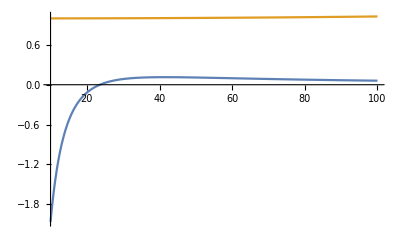

```mathematica
func := Re[ftaub taub];
funct := (taut ftau)
Checktau = Plot[ {func,funct},{Mpsa,10,100}]
```

```mathematica
Models
```

```mathematica
M1 :=  {Cf ->  2.2, Kg ->  -7.2, Kw ->7.6, Kb ->  2.8,  fa -> 1, Kaa -> 10.4}
M2 :=  {Cf ->  2.6, Kg ->  -8.7, Kw ->12., Kb ->  5.9,   fa -> 1,Kaa -> 17.9}
M3 :=  {Cf ->  2.2, Kg ->  -6.3, Kw -> 8.7, Kb ->  -8.2, fa -> 1,Kaa -> 0.5}
M4 :=  {Cf ->  1.5, Kg ->  -11., Kw ->12., Kb ->  -17., fa -> 1,Kaa -> -5.0}
M5 :=  {Cf ->  1.5, Kg ->  -4.9, Kw ->3.6, Kb ->  0.40, fa -> 1,Kaa -> 4.0}
M6 :=  {Cf ->  1.5, Kg ->  -4.9, Kw ->4.4, Kb ->  1.1, fa -> 1,Kaa -> 5.5}
M7 :=  {Cf ->  2.6, Kg ->  -8.7, Kw ->13., Kb ->  7.3, fa -> 1,Kaa -> 20.3}
M8 :=  {Cf ->  1.9, Kg ->  -1.6, Kw ->1.9, Kb ->  -2.3, fa -> 1,Kaa -> -0.4}
M9 :=  {Cf ->  0.7, Kg ->  -10., Kw ->5.6, Kb ->  -22., fa -> 1,Kaa -> -16.4}
M10 := {Cf ->  0.7, Kg ->  -9.4, Kw ->5.6, Kb ->  -19., fa -> 1,Kaa -> -13.4}
M11 := {Cf ->  1.7, Kg ->  -3.3, Kw ->3.3, Kb ->  -5.5, fa -> 1,Kaa -> -2.2}
M12 := {Cf ->  1.8, Kg ->  -4.1, Kw -> 4.6, Kb ->  -6.3, fa -> 1,Kaa -> -1.7}
```

```mathematica
Params
```

```mathematica
αsr:=12 Pi/(23 Log[Mpsa^2/.226^2])(1-6((153-19*5)/23^2)(Log[Log[Mpsa^2/.226^2]])/Log[Mpsa^2/.226^2])
```

```mathematica
Kgeff := ( Kg ) - Cf taut ftau  + Cf taub ftaub; (* - due to sign convention in Gabriele's paper! *);
Kγeff := Kaa - (4/3)Cf taut ftau + (1/3)Cf taub ftaub;
```

```mathematica
Partial widths
```

```mathematica
Γττ:=  PartialWidth[{psa,ta,tabar}];(* /.{Mpsa -> 10.}/.M12*)
Γee :=  PartialWidth[{psa,e,ebar}];
Γμμ :=  PartialWidth[{psa,mu,mubar}];
Γuu:=  PartialWidth[{psa,u,ubar}];
Γdd:=  PartialWidth[{psa,d,dbar}];
Γss:=  PartialWidth[{psa,s,sbar}];
Γcc:=  PartialWidth[{psa,c,cbar}];
Γbb:=  PartialWidth[{psa,b,bbar}];
Γγγ := α^2 Abs[Kγeff]^2 Mpsa^3 /(64 π^3);
Γhad := αsr^2(1+(97/4-7*3/6)*αsr/Pi) Abs[Kgeff]^2 Mpsa^3 /(8 π^3); 
Γfull :=Γττ + Γee +Γμμ +Γuu + Γdd + Γss + Γcc + Γbb + Γγγ +Γhad;
```

```mathematica
BRττ:=  Γττ /Γfull ; 
BRμμ := Γμμ /Γfull; 
BRee :=  Γee/Γfull ; 
BRuu := Γuu/Γfull ;
BRdd := Γdd/Γfull ;
BRcc := Γcc/Γfull ;
BRss := Γss/Γfull ;
BRbb :=  Γbb /Γfull ;
BRcc :=  Γcc /Γfull;
BRγγ :=  Γγγ /Γfull ;BRhad:=  Γhad /Γfull ;
```

```mathematica
N[BRττ]/.M12/.{Mpsa-> 10}
N[BRττ]/.M12/.{Mpsa-> 20}
N[BRττ]/.M12/.{Mpsa-> 30}
N[BRττ]/.M12/.{Mpsa-> 40}
N[BRττ]/.M12/.{Mpsa-> 50}
N[BRττ]/.M12/.{Mpsa-> 60}
N[BRττ]/.M12/.{Mpsa-> 70}
N[BRττ]/.M12/.{Mpsa-> 80}
N[BRττ]/.M12/.{Mpsa-> 90}
N[BRττ]/.M12/.{Mpsa-> 100}
```

0.057875

0.0343752

0.0289294

0.0243583

0.0205064

0.0173395

0.0147644

0.0126727

0.0109661

0.00956378

```mathematica
N[BRbb]/.M12/.{Mpsa-> 10}
N[BRbb]/.M12/.{Mpsa-> 20}
N[BRbb]/.M12/.{Mpsa-> 30}
N[BRbb]/.M12/.{Mpsa-> 40}
N[BRbb]/.M12/.{Mpsa-> 50}
N[BRbb]/.M12/.{Mpsa-> 60}
N[BRbb]/.M12/.{Mpsa-> 70}
N[BRbb]/.M12/.{Mpsa-> 80}
N[BRbb]/.M12/.{Mpsa-> 90}
N[BRbb]/.M12/.{Mpsa-> 100}
```

0.443333

0.647069

0.580646

0.498856

0.423758

0.360037

0.307444

0.264375

0.229061

0.199949

```mathematica
Plots
```

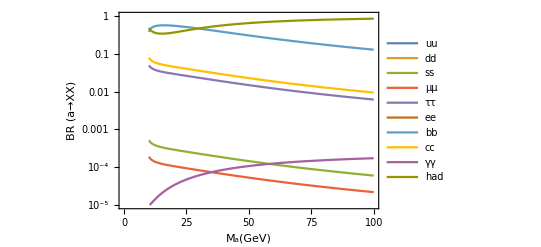

AllBRplots1.eps

```mathematica
AllBRplots1 = LogPlot[{BRuu/.M1,BRdd/.M1,BRss/.M1,BRμμ/. M1,BRττ/.M1, BRee/.M1,BRbb/.M1, BRcc/.M1, BRγγ/.M1, BRhad/.M1},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.00001,1}},PlotLegends->{"uu","dd","ss","μμ","ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots1.eps",AllBRplots1]
```

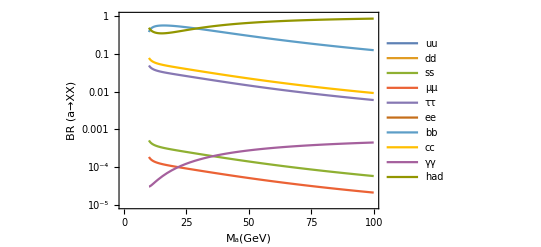

AllBRplots2.eps

```mathematica
AllBRplots2 = LogPlot[{BRuu/.M2,BRdd/.M2,BRss/.M2,BRμμ/. M2,BRττ/.M2, BRee/.M2,BRbb/.M2, BRcc/.M2, BRγγ/.M2, BRhad/.M2},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.00001,1}},PlotLegends->{"uu","dd","ss","μμ","ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots2.eps",AllBRplots2]
```

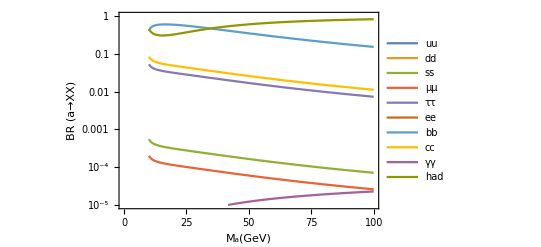

AllBRplots3.eps

```mathematica
AllBRplots3 = LogPlot[{BRuu/.M3,BRdd/.M3,BRss/.M3,BRμμ/. M3,BRττ/.M3, BRee/.M3,BRbb/.M3, BRcc/.M3, BRγγ/.M3, BRhad/.M3},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.00001,1}},PlotLegends->{"uu","dd","ss","μμ","ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots3.eps",AllBRplots3]
```

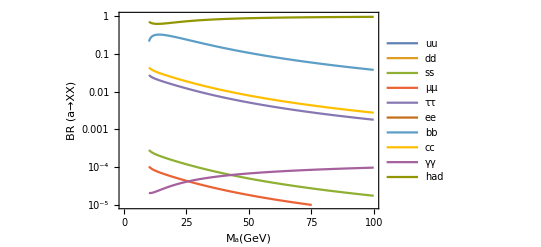

AllBRplots4.eps

```mathematica
AllBRplots4 = LogPlot[{BRuu/.M4,BRdd/.M4,BRss/.M4,BRμμ/. M4,BRττ/.M4, BRee/.M4,BRbb/.M4, BRcc/.M4, BRγγ/.M4, BRhad/.M4},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.00001,1}},PlotLegends->{"uu","dd","ss","μμ","ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots4.eps",AllBRplots4]
```

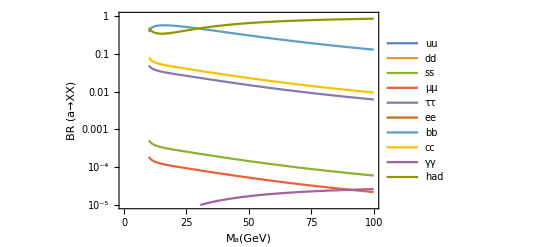

AllBRplots5.eps

```mathematica
AllBRplots5 = LogPlot[{BRuu/.M5,BRdd/.M5,BRss/.M5,BRμμ/. M5,BRττ/.M5, BRee/.M5,BRbb/.M5, BRcc/.M5, BRγγ/.M5, BRhad/.M5},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.00001,1}},PlotLegends->{"uu","dd","ss","μμ","ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots5.eps",AllBRplots5]
```

```mathematica
AllBRplots6 = LogPlot[{BRττ/.M6,BRee/.M6, BRbb/.M6, BRcc/.M6, BRγγ/.M6, BRhad/.M6},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.0001,1}}, PlotLegends->{"ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots6.eps",AllBRplots6]
```

AllBRplots6.eps

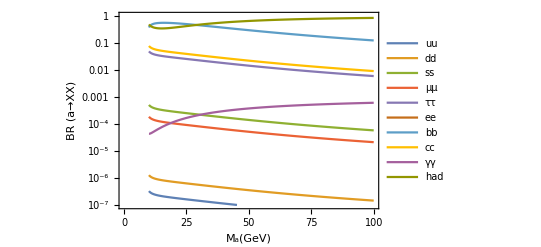

AllBRplots7.eps

```mathematica
AllBRplots7 = LogPlot[{BRuu/.M7,BRdd/.M7,BRss/.M7,BRμμ/. M7,BRττ/.M7,BRee/.M7, BRbb/.M7, BRcc/.M7, BRγγ/.M7, BRhad/.M7},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.0000001,1}},PlotLegends->{"uu","dd","ss","μμ","ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots7.eps",AllBRplots7]
```

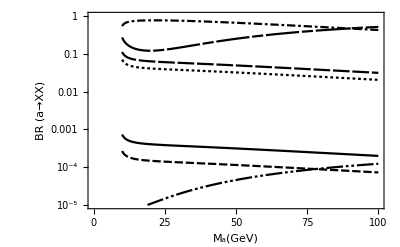

AllBRplots8.eps

```mathematica
AllBRplots8 = LogPlot[{BRss/.M8,BRμμ/. M8,BRττ/.M8, BRbb/.M8, BRcc/.M8, BRγγ/.M8, BRhad/.M8},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.00001,1}}(*,PlotLegends->{"ss","μμ","ττ",  "bb", "cc", "γγ", "had"}*),PlotTheme->"Monochrome"]
Export["AllBRplots8.eps",AllBRplots8]
```

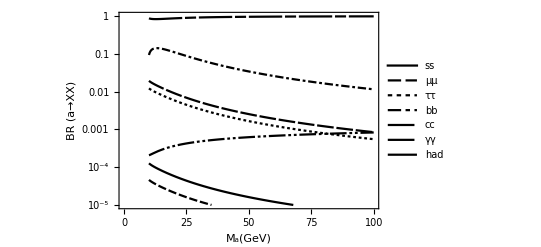

AllBRplots9.eps

```mathematica
AllBRplots9 = LogPlot[{BRss/.M9,BRμμ/. M9,BRττ/.M9, BRbb/.M9, BRcc/.M9, BRγγ/.M9, BRhad/.M9},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.00001,1}},PlotLegends->{"ss","μμ","ττ", "bb", "cc", "γγ", "had"},PlotTheme->"Monochrome"]
Export["AllBRplots9.eps",AllBRplots9]
```

```mathematica
AllBRplots10 = LogPlot[{BRττ/.M10,BRee/.M10, BRbb/.M10, BRcc/.M10, BRγγ/.M10, BRhad/.M10},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.0001,1}}, PlotLegends->{"ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots10.eps",AllBRplots10]
```

AllBRplots10.eps

```mathematica
AllBRplots11 = LogPlot[{BRττ/.M11,BRee/.M11, BRbb/.M11, BRcc/.M11, BRγγ/.M11, BRhad/.M11},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.0001,1}}, PlotLegends->{"ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots11.eps",AllBRplots11]
```

AllBRplots11.eps

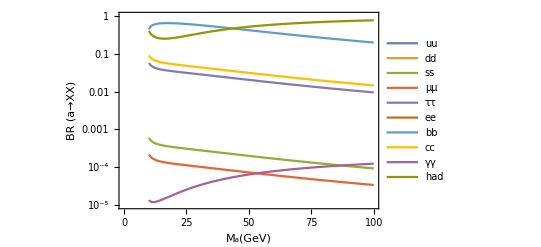

AllBRplots12.eps

```mathematica
AllBRplots12 = LogPlot[{BRuu/.M12,BRdd/.M12,BRss/.M12,BRμμ/. M12,BRττ/.M12, BRee/.M12,BRbb/.M12, BRcc/.M12, BRγγ/.M12, BRhad/.M12},{Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> XX)},PlotRange->{{0,100},{0.00001,1}},PlotLegends->{"uu","dd","ss","μμ","ττ", "ee", "bb", "cc", "γγ", "had"}]
Export["AllBRplots12.eps",AllBRplots12]
```

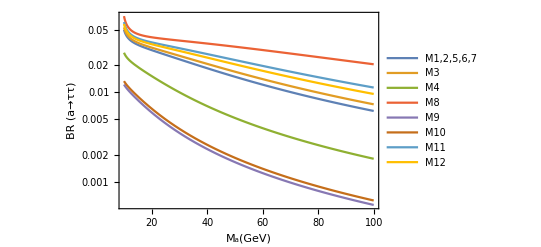

```mathematica
BRττplot = LogPlot[{BRττ/.M1,BRττ/.M3,BRττ/.M4,BRττ/.M8,BRττ/.M9,BRττ/.M10,BRττ/.M11,BRττ/.M12} , {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> ττ)},PlotLegends->{"M1,2,5,6,7","M3", "M4","M8", "M9", "M10", "M11", "M12"}(*,PlotTheme->"Monochrome"*)]
```

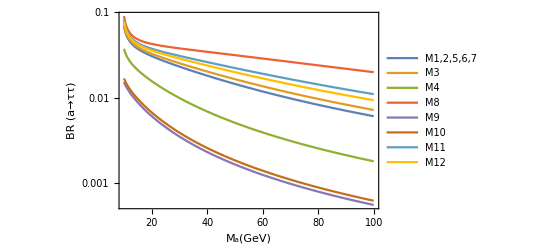

```mathematica
Export["BRtautau_monochrome.eps",BRττplot]
```

BRtautau_monochrome.eps

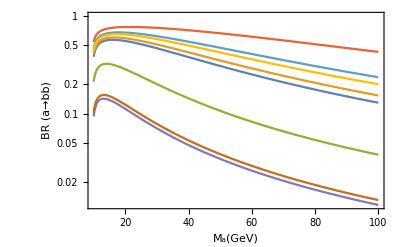

```mathematica
(*BRbbplot = LogPlot[{BRbb/.M1,  BRbb/.M2,BRbb/.M3,BRbb/.M4,BRbb/.M5,BRbb/.M6,BRbb/.M7,BRbb/.M8,BRbb/.M9,BRbb/.M10,BRbb/.M11,BRbb/.M12} , {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> bb)},PlotStyle-> { DotDashed,DotDashed,DotDashed,DotDashed,Dashing[{l1,s,l1,s,l2,s}],Dashing[{l1,s,l1,s,l2,s}],Dashing[{s,s,l1,s,l1}],Dashing[Tiny],Dashing[Large],Dotted,Solid,Dashing[{s,s,l1,s,l1}]}(*,PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}*)]*)
BRbbplot = LogPlot[{BRbb/.M1,BRbb/.M3,BRbb/.M4,BRbb/.M8,BRbb/.M9,BRbb/.M10,BRbb/.M11,BRbb/.M12} , {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> bb)}(*,PlotTheme->"Monochrome"*)]
```

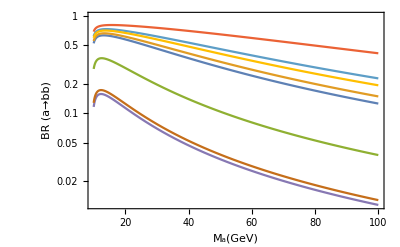

```mathematica
Export["BRbb_monochrome.eps",BRbbplot]
```

BRbb_monochrome.eps

```mathematica
(* {BRγγ/.M1,BRγγ/.M2,BRγγ/.M3,BRγγ/.M4,BRγγ/.M5,BRγγ/.M6,BRγγ/.M7,BRγγ/.M8,BRγγ/.M9,BRγγ/.M10,BRγγ/.M11,BRγγ/.M12} *)
```

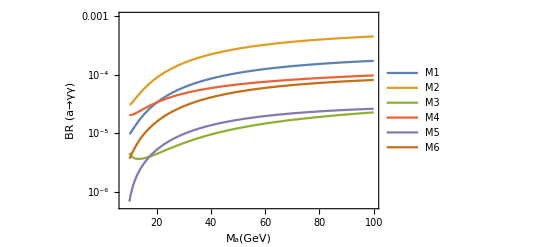

```mathematica
BRγγplot = LogPlot[ {BRγγ/.M1,BRγγ/.M2,BRγγ/.M3,BRγγ/.M4,BRγγ/.M5,BRγγ/.M6(*,BRγγ/.M7,BRγγ/.M8,BRγγ/.M9,BRγγ/.M10,BRγγ/.M11,BRγγ/.M12*)}, {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> γγ)},PlotRange->{{8,100},{0.0000006,0.001}},PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6"(*, "M7", "M8", "M9", "M10", "M11", "M12"*)}(*,PlotTheme->"Monochrome"*)]
```

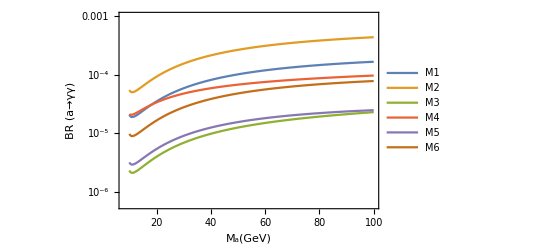

```mathematica
Export["BRgammagamma_monochrome_1-6.eps",BRγγplot]
```

BRgammagamma_monochrome_1-6.eps

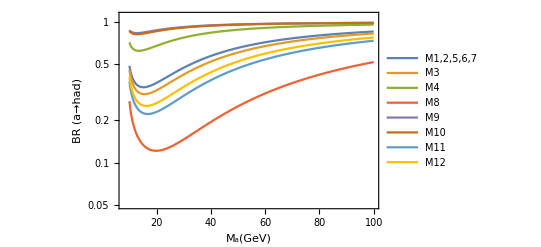

```mathematica
BRhadplot = LogPlot[{BRhad/.M1,BRhad/.M3,BRhad/.M4,BRhad/.M8,BRhad/.M9,BRhad/.M10,BRhad/.M11,BRhad/.M12} , {Mpsa, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> had)}, 
PlotRange->{{8,100},{0.05,1.1}},PlotLegends->{"M1,2,5,6,7", "M3", "M4", "M8", "M9", "M10", "M11", "M12"}(*,PlotTheme->"Monochrome"*)]
```

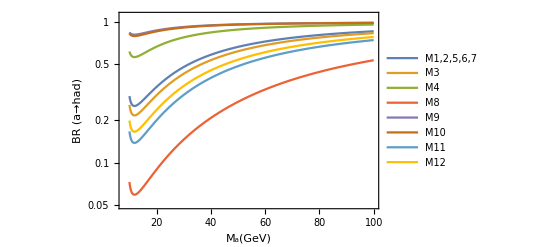

```mathematica
Export["BRhad_monochrome.eps",BRhadplot]
```

BRhad_monochrome.eps

## FeynArts

```mathematica
WriteFeynArtsOutput[LSM + LPSeudo, FlavorExpand->SU2W, FlavorExpand->SU2D]
```

```mathematica
<<FeynArts`
<< FormCalc`
model=FileNameJoin[{NotebookDirectory[],"CHpsuedo_FA","CHpseudo_FA"}];
```